## 多层神经网络

```mathematica
σ[x_]:=1/(1+Power[ⅇ, -x]);
dσ[x_]:=σ[x](1-σ[x]);
SetAttributes[dσ,Listable];
SetAttributes[σ,Listable];
```

```mathematica
(*要求X是m×r的矩阵, Y是p×r的矩阵, n是隐藏层神经元的个数, l-1是隐藏层的层数*)
MBPNN[X__,Y__,n_,l_]:=Module[{r=0,m=0,p=0,Error=100,err={},W={},b={},er={},a={},z={},δ={},η=0.5,iterMax=10000},
{m,r}=Dimensions[X];{p,r}=Dimensions[Y];
AppendTo[W,RandomReal[{-1,1},{n,m}]];
(AppendTo[W,RandomReal[{-1,1},{n,n}]])&/@Range[2,l-1];
AppendTo[W,RandomReal[{-1,1},{p,n}]];
(AppendTo[b,RandomReal[{-1,1},{n,1}]])&/@Range[1,l-1];
AppendTo[b,RandomReal[{-1,1},{p,1}]];
(*********************************************************************)
er={Table[1,{i,r}]};

While[Error>0.001&&iterMax>0,
iterMax--;
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
Error=1/2 Norm[a[[l]]-Y,"Frobenius"]^2;
AppendTo[err,Error];
PrependTo[δ,(a[[l]]-Y)*dσ[z[[l]]]];
PrependTo[δ,(Transpose[W[[#+1]]].δ[[1]])*dσ[z[[#]]]]&/@Table[i,{i,l-1,1,-1}];
(W[[#]]=W[[#]]-η δ[[#]].Transpose[a[[#-1]]])&/@Range[2,l];
W[[1]]=W[[1]]-η δ[[1]].Transpose[X];
(b[[#]]=b[[#]]-η δ[[#]].Transpose[er])&/@Range[l];
a={};z={};δ={};
];
{W,b,err}
]
```

```mathematica
predict[W__,b__,X__]:=Module[{z={},a={},l=Length[W],r=Length[X[[1]]],er={}},
er={Table[1,{i,r}]};
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
a[[l]]
]
```

### 经过batch的神经网络训练

{{1.06061,1.89192,3.05017},{6.99931,8.15276,8.65253}}

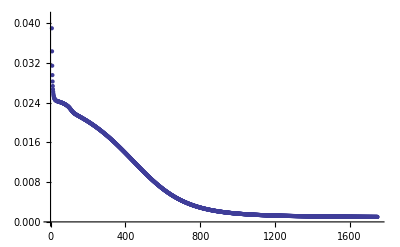

```mathematica
X={{1,2,3},{4,5,6},{7,8,9},{10,11,12}};
Y={{1,2,3},{7,8,9}}/9;
res=MBPNN[X,Y,8,3];
predict[res[[1]],res[[2]],X]*9
ListPlot[res[[3]]]
```

## debug area

```mathematica
σ[x_]:=1/(1+Power[ⅇ, -x]);
dσ[x_]:=σ[x](1-σ[x]);
SetAttributes[dσ,Listable];
SetAttributes[σ,Listable];
```

```mathematica
predict[W__,b__,X__]:=Module[{z={},a={},l=Length[W],r=Length[X[[1]]],er={}},
er={Table[1,{i,r}]};
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
a[[l]]
]
```

```mathematica
data=Import["C:\\Users\\PC\\Desktop\\data.txt",CharacterEncoding->"UTF-8"];
splitdata=StringSplit[data,"\n"];
vectordata=ToExpression@StringSplit[#,","]&/@splitdata;
Xs=Transpose[ToExpression@vectordata[[All,1;;-2]]];
Ys={vectordata[[All,-1]]};
```

```mathematica
data=Import["C:\\Users\\PC\\Documents\\WeChat Files\\shuxuejia0805\\Files\\ghf_interest.txt"];
data=StringSplit[data,"\n"];
data=(StringSplit[#,","])&/@data;
data=(ToExpression[#]&/@#)&/@data;
data=Join[Select[data,Length[#]==43&&#[[-1]]==0&][[1;;600]], Select[data,Length[#]==43&&#[[-1]]==1&]];
Xs=Transpose[Select[data,#[[-1]]<2&][[All,1;;-2]]];
Ys={Select[data,#[[-1]]<2&][[All,-1]]};
```

```mathematica
Xs//Dimensions
```

{24,17419}

```mathematica
batch=20;
n=5;l=3;
{r=0,m=0,p=0,Error=100,W={},b={},er={},a={},z={},δ={}};
{m,r}=Dimensions[Xs];{p,r}=Dimensions[Ys];
AppendTo[W,RandomReal[{-1,1},{n,m}]];
(AppendTo[W,RandomReal[{-1,1},{n,n}]])&/@Range[2,l-1];
AppendTo[W,RandomReal[{-1,1},{p,n}]];
(AppendTo[b,RandomReal[{-1,1},{n,1}]])&/@Range[1,l-1];
AppendTo[b,RandomReal[{-1,1},{p,1}]];
(*********************************************************************)
er={Table[1,{i,batch}]};
minW=W;minb=b;
```

```mathematica
iterMax=10000;
η=0.5/batch;
err={};
minerr=Error;
Dynamic[{(MatrixPlot[#])&/@W,iterMax,minerr,ListLinePlot[err]}]

While[Error>0.000001&&iterMax>0,
iterMax--;
sample=RandomSample[Range[r],batch];
X=Xs[[All,sample]];
Y=Ys[[All,sample]];
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
Error=1/2 Norm[a[[l]]-Y,"Frobenius"]^2;
If[minerr>Error,minerr=Error;AppendTo[err,Error];minW=W;minb=b];
PrependTo[δ,(a[[l]]-Y)*dσ[z[[l]]]];
PrependTo[δ,(Transpose[W[[#+1]]].δ[[1]])*dσ[z[[#]]]]&/@Table[i,{i,l-1,1,-1}];
(W[[#]]=W[[#]]-η δ[[#]].Transpose[a[[#-1]]])&/@Range[2,l];
W[[1]]=W[[1]]-η δ[[1]].Transpose[X];
(b[[#]]=b[[#]]-η δ[[#]].Transpose[er])&/@Range[l];
a={};z={};δ={};
];
```

11668

12293

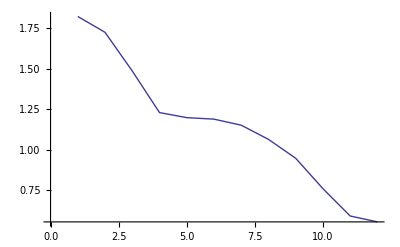

```mathematica
Length[Select[Transpose[{Boole[#>0.5]&/@predict[W,b,Xs][[1]],Ys[[1]]}],#[[1]]==#[[2]]&]]
Length[Select[Transpose[{Boole[#>0.5]&/@predict[minW,minb,Xs][[1]],Ys[[1]]}],#[[1]]==#[[2]]&]]
ListLinePlot[err]
```

```mathematica
12408/17419//N
```

0.712326

```mathematica
Length@Select[Ys[[1]],#==0&]
```

139267